```mathematica
ClearAll["Global`*"]
$VersionNumber
```

12.3

## CMF distribution

```mathematica
ClearAll["Global`*"]
```

```mathematica
AngleLine[a_]:={{Re[Exp[I a Degree]],Im[Exp[I a Degree]]},{Re[Exp[I (a+180) Degree]],Im[Exp[I (a+180) Degree]]}};
dist[x_,sig_,n_]:=Module[{x0=x,sig0=sig,n0=n},
AngleLine[a_]:={{Re[Exp[I a Degree]],Im[Exp[I a Degree]]},{Re[Exp[I (a+180) Degree]],Im[Exp[I (a+180) Degree]]}};
p1=ListLinePlot[AngleLine/@RandomVariate[NormalDistribution[x0,sig0],n0],PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1,ImageSize->Medium,PlotStyle->Darker[Green],Ticks->None,TicksStyle->Directive["Label", 14]];
p2=Plot[PDF[NormalDistribution[x0,sig0],y],{y,-300,300},PlotRange->All,ImageSize->Medium];
{p1,p2}
]
```

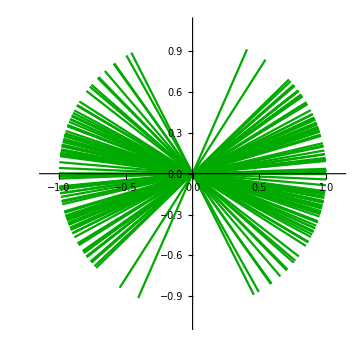
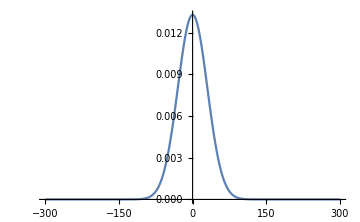

```mathematica
dist[0,30,100](*fiber direction, standard deviation, number of fibers*)
```

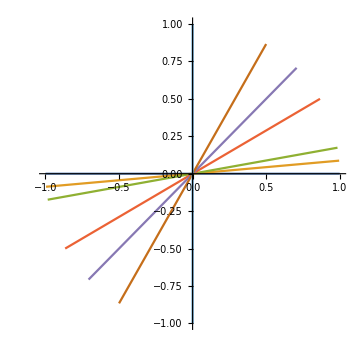

```mathematica
ListLinePlot[AngleLine/@{0,5,10,30,45,60,90},AspectRatio->1,ImageSize->Medium]
```

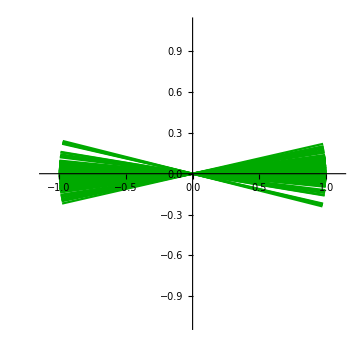
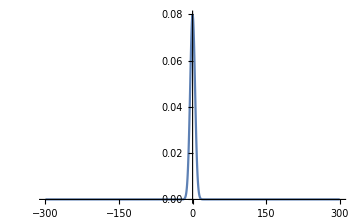
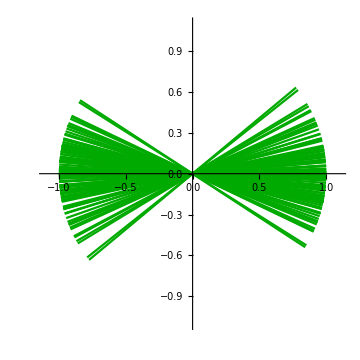
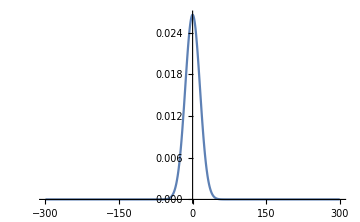
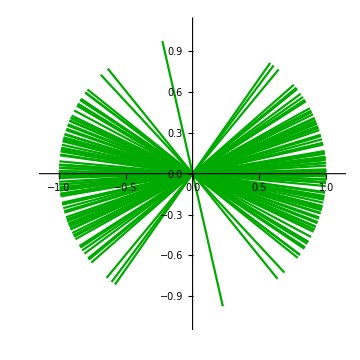
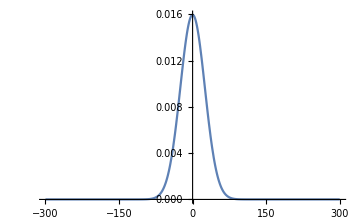

```mathematica
Table[dist[0,x,100],{x,5,25,10}]
```